## Direct Traslation in Polar Corrdinate

```mathematica
{t,r}->{t',r'}
```

```mathematica
r1[t_]:=√(t+1)
r2[t_]:=0.5
```

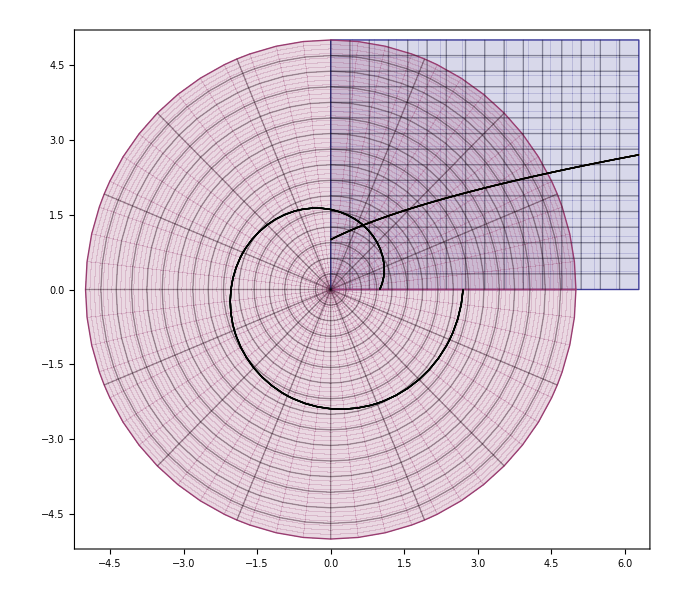

```mathematica
ParametricPlot[
{
{t,r},
{r Cos[t],r Sin[t]},
{t,r1[t]},
{r1[t] Cos[t],r1[t]Sin[t]}
},{t,0,2π},{r,0,5}]
```

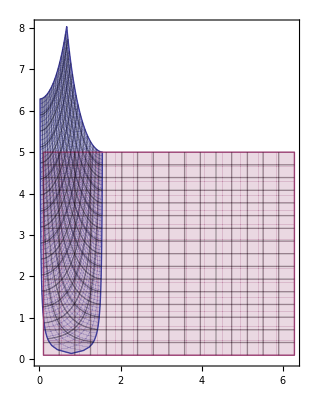

```mathematica
ParametricPlot[
{
{Arg[x+y ⅈ],√(x^2+y^2)},
{x,y}
},{x,0.1,2π},{y,0.1,5}]
```

## Ellipse in Polar Coordinate of focus

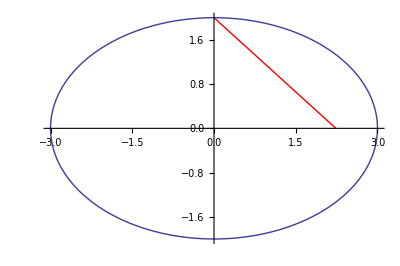

```mathematica
Show[
ParametricPlot[{3Cos[t],2Sin[t]},{t,0,2π}],
ListPlot[{{0,2},{√5,0}},Joined->True,PlotStyle->Red]
]
```

e = ellipticity = √(1-(b/a)^2)
f = focal length = e a

```mathematica
Solve[{e^2==1-B/a^2,f==e a},{B,f}]
```

{{B→-a^2 (-1+e^2),f→a e}}

```mathematica
x^2/a^2+y^2/B/.{B->a^2-a^2 e^2}
```

x^2/a^2+y^2/(a^2-a^2 e^2)

```mathematica
%/.{x->r Cos[t]-a e,y->r Sin[t]}
```

(-a e+r Cos[t])^2/a^2+(r^2 Sin[t]^2)/(a^2-a^2 e^2)

```mathematica
Solve[(-a e+r Cos[t])^2/a^2+(r^2 Sin[t]^2)/(a^2-a^2 e^2)==1,r]//TrigExpand//Simplify
```

{{r→-(2 (√(a^2 (-1+e^2)^2)-a e (-1+e^2) Cos[t]))/(-2+e^2+e^2 Cos[2 t])},{r→(2 (√(a^2 (-1+e^2)^2)+a e (-1+e^2) Cos[t]))/(-2+e^2+e^2 Cos[2 t])}}

```mathematica
(2 (√(a^2 (-1+e^2)^2)+a e (-1+e^2) Cos[t]))/(-2+e^2+e^2 Cos[2 t])/.{Cos[2t]->2 A^2-1,Cos[t]->A,√(a^2 (-1+e^2)^2)->a (-1+e^2)}//FullSimplify
```

```mathematica
(a (-1+e^2))/(-1+A e)/.{A->Cos[t]}
```

(a (-1+e^2))/(-1+e Cos[t])

```mathematica
Manipulate[PolarPlot[(a(1-e^2))/(1-e Cos[t]),{t,0,2π},PlotRange->{{-1,2},{-1,1}}],{e,0,1},{a,0,2}]
```

```mathematica
Manipulate[Plot[(a(1-e^2))/(1-e Cos[t]),{t,0,2π},PlotRange->{{0,2π},{-1,2}}],{e,0,1},{a,0,2}]
```

## Ellipse in Polar Coordinate of origin

```mathematica
Manipulate[PolarPlot[(√(a^2 (1-e^2)))/(√(1-e^2 Cos[t]^2)),{t,0,2π},PlotRange->{{-1,1},{-1,1}}],{e,0,1},{a,0,2}]
```

```mathematica
Manipulate[Plot[(√(a^2 (1-e^2)))/(√(1-e^2 Cos[t]^2)),{t,0,2π},PlotRange->{{0,2π},{-1,2}}],{e,0,1},{a,0,2}]
```